```mathematica
(* note *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->False};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[Bucketed], file = file <>"g"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]==False, data=Flatten[data]];
Return[data];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

PlotEnergyBuckets[s_,M_,n_]:=Module[{data,i,list},
data=LoadAndBucketEnergies[s,M,n];
list=Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}];
(*Print[list];*)
ListPlot[list]
];

PlotEnergyBuckets[s_,M_]:=Module[{data},
data=LoadEigenEnergies[s,M,Bucketed->True];
ListPlot[data]
];
```

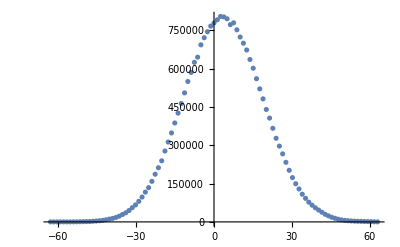

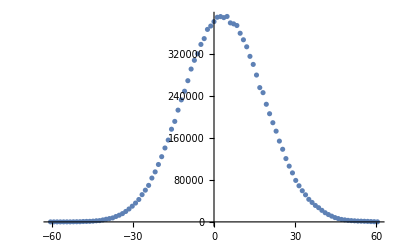

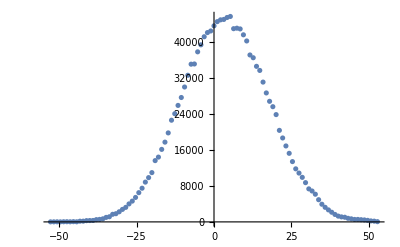

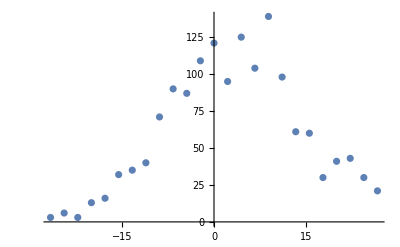

```mathematica
PlotEnergyBuckets[1,25]
PlotEnergyBuckets[1,24]
PlotEnergyBuckets[1,21]
PlotEnergyBuckets[1,11,25]
```